```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY197/sec_int_data/368nm.dat"]
```

{{1.50189,-0.810108},{1.45414,-0.777181},{1.33983,-0.70526},{1.30748,-0.700756},{1.27821,-0.678692},{1.24682,-0.718691},{1.22351,-0.912199},{1.20659,-1.07972},{1.18213,-1.39934},{1.16419,-1.74503},{1.15263,-1.93676},{1.13304,-2.38147},{1.09662,-0.739862},{1.09807,-0.831467},{1.10207,-0.832294},{1.10747,-0.817441},{1.11401,-0.809411},{1.12685,-0.765997},{1.13867,-0.738647},{1.15401,-0.739987},{1.16573,-0.76688},{1.20258,-0.778378},{1.26466,-0.771952},{1.30748,-0.826244},{1.33983,-0.878754},{1.37936,-0.897175}}

-2.11404+0.941407 x

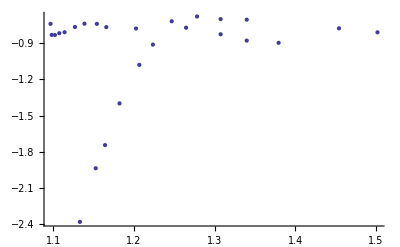

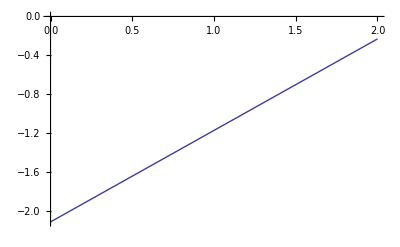

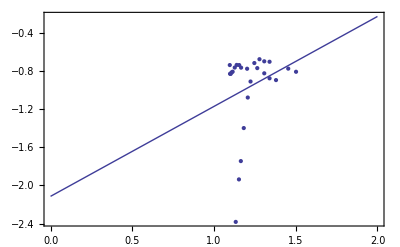

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```